# Homework 3

Make a FFT procedure by a myfft.m function, to validate it:
let x(t)=0.15sin(2πf_1t)+sin(2π f_2t)-0.1sin(2π f_3t), f_1=1Hz, f_2=2Hz, f_3=3Hz, f_s=32Hz;
plot the spectrum of signal with N=64 respectively by myfft(xn, N) function;

某一标准正弦信号受到较小的随机干扰，采样后的数据xn为
x1=[ 1.3008  1.0325  1.3154  0.3463  0.1349 -0.8776 -0.1335 -0.1649];
x2=[ 0.4608  0.7184  1.0532 -0.6689 -0.7790 -1.8854 -1.0160  0.6986];
x3=[ 0.6367  0.8822 -0.6003  0.0703 -0.2433  0.9322  1.2893  1.8318];
x4=[ 1.8853 -0.5030  0.5779 -0.7427  0.5680  0.6290  0.7174  0.3087];
x5=[-0.0794 -1.1864 -1.0735 -0.1660  0.8689  2.0009  0.7683 -0.8091];
x6=[-0.1990 -0.9802 -1.3392 -0.3247  1.2939  0.1609 -0.0482 -0.9174];
x7=[-1.7593 -2.2465  0.0998  0.9753  0.6950  0.2317  1.4903 -1.1632];
x8=[-0.1584  1.0070  1.3032  0.4372  1.4021 -0.3828 -1.6361 -0.4863];
xn=[x1 x2 x3 x4 x5 x6 x7 x8];
采样速率为32Hz，调用myfft子程序进行频谱分析，计算出正弦信号的频率值

## FFT实现:

```mathematica
bitReverse[n_?IntegerQ]:=((FromDigits[#,2]&)@*Reverse@*(IntegerDigits[#,2,n]&))
```

```mathematica
implFFT=Compile[{{x,_Complex,1}},
With[{n=Length[x],m=Log2@Length[x]},
Module[{A=x},
Do[With[{j=bitReverse[m][i]}, (* 倒序 *)
If[i<j,
A⟦{1+i,1+j}⟧=A⟦{1+j,1+i}⟧ ; 
] (* 交换 *)
],{i,1,n-2}
];
Do[With[{b=2^(l-1)},
Do[With[{p=j*2^(m-l)},
Do[ (* 蝶形运算 *)
A⟦{1+k,1+k+b}⟧={A⟦1+k⟧+A⟦1+k+b⟧*Exp[-2π*ⅈ*p/n],A⟦1+k⟧-A⟦1+k+b⟧*Exp[-2π*ⅈ*p/n]};
,{k,j,n-1,2*b}
]
],{j,0,b-1}
]
],{l,1,m}
];
A]
]
];
```

```mathematica
implDFT[x_?VectorQ]:=With[{n=Length[x]},
(Exp[-2π*ⅈ/n]^Table[i*j,{i,0,n-1},{j,0,n-1}]).x (* '.'是点乘 *)
]
```

```mathematica
myFFT[x_/;(VectorQ[x]&&IntegerQ@Log2@Length[x])]:=implFFT[N[x]](* 当长度合适时，采用FFT *)
myFFT[x_?VectorQ]:=implDFT[N[x]](* 否则用普通的DFT *)
```

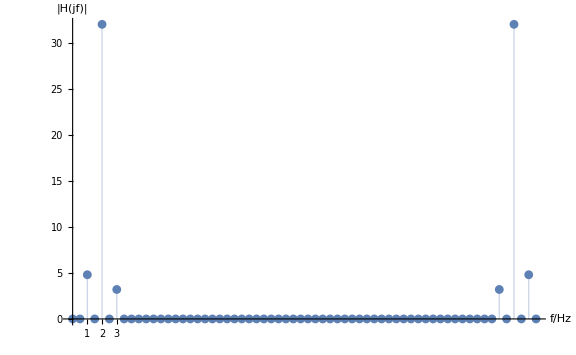

```mathematica
With[{f1=1,f2=2,f3=3,fs=32,n=64},
ListPlot[
Abs@myFFT[Table[0.15Sin[2π*f1*t]+Sin[2π*f2*t]-0.1Sin[2π*f3*t],{t,0,(n-1)/fs,1/fs}]],
Filling->Axis,AxesLabel->{"f/Hz","|H(jf)|"},
DataRange->{0,fs*(n-1)/n},
Ticks->{{f1,f2,f3},Automatic},
ImageSize->Large,PlotRange->Full
]
]
```

```mathematica
x={1.3008,1.0325,1.3154,0.3463,0.1349,-0.8776,-0.1335,-0.1649,
0.4608,0.7184,1.0532,-0.6689,-0.7790,-1.8854,-1.0160,0.6986,
0.6367,0.8822,-0.6003,0.0703,-0.2433,0.9322,1.2893,1.8318,
1.8853,-0.5030,0.5779,-0.7427,0.5680,0.6290,0.7174,0.3087,
-0.0794,-1.1864,-1.0735,-0.1660,0.8689,2.0009,0.7683,-0.8091,
-0.1990,-0.9802,-1.3392,-0.3247,1.2939,0.1609,-0.0482,-0.9174,
-1.7593,-2.2465,0.0998,0.9753,0.6950,0.2317,1.4903,-1.1632,
-0.1584,1.0070,1.3032,0.4372,1.4021,-0.3828,-1.6361,-0.4863};
```

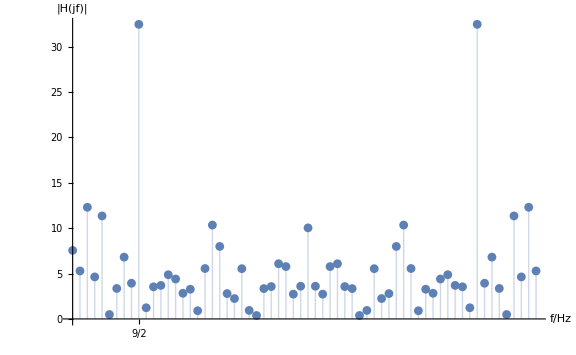

```mathematica
With[{fs=32,n=Length[x]},
ListPlot[
Abs@myFFT[x],
Filling->Axis,AxesLabel->{"f/Hz","|H(jf)|"},
DataRange->{0,fs*(n-1)/n},
Ticks->{{9/2},Automatic},
ImageSize->Large,PlotRange->Full
]
]
```

可以看到在f = 9/2 处有一明显尖峰，故原正弦信号的频率应为 9/2 Hz。

## 补充：对FFT、DFT以及Mathematica内建的Fourier函数的简单性能比较

```mathematica
ListLogLogPlot[
Table[
Table[{2^n,Module[{x=Table[Sin[x],{x,1,2^n}]},
ClearSystemCache[];First@Timing[tf[x];]
]},
{n,1,12}],
{tf,{implFFT,implDFT,Fourier}}
],Joined->True,AxesLabel->{"N","t/s"},
PlotRange->All,PlotLabels->{"FFT","DFT","Builtin"}
]
```

-Graphics-

```mathematica
baseMemory=MemoryInUse[];
ListLogLogPlot[
Table[
Table[{2^n,Module[{x=Table[Sin[x],{x,1,2^n}]},
ClearSystemCache[];tf[x];(MemoryInUse[]-baseMemory)
]},
{n,1,12}],
{tf,{implFFT,implDFT,Fourier}}
],Joined->True,AxesLabel->{"N","Memory/Byte"},
PlotRange->All,PlotLabels->{"FFT","DFT","Builtin"}
]
```

-Graphics-